```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
metalvl2={Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## E

1 , Run 10 #: 12693

0.009±0.018

2 , Run 10 #: 12695

-0.01±0.012

3 , Run 10 #: 12697

0.011±0.011

4 , Run 10 #: 12704

0.001±0.014

5 , Run 10 #: 12707

-0.014±0.012

8 , Run 10 #: 12772

0.135±0.046

9 , Run 10 #: 12773

-0.192±0.044

11 , Run 10 #: 12775

0.19±0.16

12 , Run 10 #: 12778

0.056±0.046

13 , Run 10 #: 12779

-0.031±0.05

14 , Run 10 #: 12780

0.027±0.058

15 , Run 20 #: 13099

17 , Run 20 #: 13103

18 , Run 20 #: 13104

20 , Run 20 #: 13107

22 , Run 20 #: 13109

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

25 , Run 20 #: 13132

26 , Run 20 #: 13133

27 , Run 20 #: 13134

29 , Run 20 #: 13136

30 , Run 20 #: 13137

31 , Run 20 #: 13138

32 , Run 20 #: 13139

33 , Run 20 #: 13140

35 , Run 20 #: 13142

36 , Run 20 #: 13146

| Estimate | Standard Error | t-Statistic | P-Value
m | 0.000298714 | 0.000479285 | 0.623249 | 0.548588
c | -0.0124571 | 0.126304 | -0.0986275 | 0.923596

| DF | SS | MS
Model | 2 | 0.00213144 | 0.00106572
Error | 9 | 0.00631756 | 0.000701951
Uncorrected Total | 11 | 0.008449 | 
Corrected Total | 10 | 0.00659022 |

1.0007

χ2_10: 1.52192

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.0000873942 | 0.000187056 | -0.467208 | 0.648085
c | 0.0182282 | 0.184436 | 0.0988324 | 0.922779

| DF | SS | MS
Model | 2 | 0.00480686 | 0.00240343
Error | 13 | 0.0547686 | 0.00421297
Uncorrected Total | 15 | 0.0595754 | 
Corrected Total | 14 | 0.0556882 |

1.00421

χ2_20: 0.740651

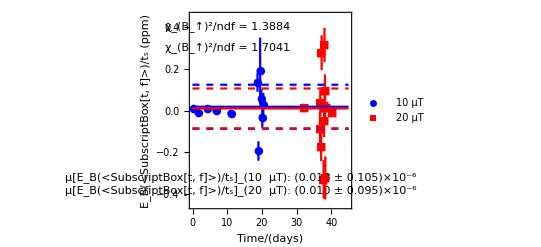

```mathematica
lvl3={};
lvl2={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
pttstfet10b={};pttstfet20b={};
For[i=1,i≤dimdesc,i++,
lvl2=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],metalvl2];
If[i==1,sttime=lvl2[[1]][[1]]];
xx=((Abs[-lvl2[[1]][[1]]+lvl2[[-1]][[1]]]/2)+Abs[lvl2[[1]][[1]]-sttime])/(24*3600);
If[(!MemberQ[{6,7,10},i]&&descdat[[i]][[6]]==10)
,
Print[i," , Run 10 #: ",descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,Sqrt[ts[[2]]^2+lvl3[[1]][[4]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
yy=1/PlusMinus[lvl3[[1]][[3]]*(descdat[[i]][[9]]*10^6/ts[[1]]),lvl3[[1]][[4]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
Print[1/yy];
If[Abs[yy[[1]]]<2 Abs[yy[[2]]]&&Abs[yy[[1]]]<200,pttstfet10b=AppendTo[pttstfet10b,{xx,{yy[[1]],yy[[2]]}}]];
fttstfet10=AppendTo[fttstfet10,{xx,lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl3[[1]][[4]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
If[(MemberQ[{15,17,18,20,22,25,26,27,29,30,31,32,33,35,36,37(*6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,34,37*)},i]&&descdat[[i]][[6]]==20)
,
Print[i," , Run 20 #: ",descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,Sqrt[ts[[2]]^2+lvl3[[1]][[4]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl3[[1]][[3]],lvl3[[1]][[4]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
yy=1/PlusMinus[lvl3[[1]][[3]]*(descdat[[i]][[9]]*10^6/ts[[1]]),lvl3[[1]][[4]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
If[Abs[yy[[1]]]<2Abs[yy[[2]]]&&Abs[yy[[1]]]<200,pttstfet20b=AppendTo[pttstfet20b,{xx,{yy[[1]],yy[[2]]}}]];
fttstfet20=AppendTo[fttstfet20,{xx,lvl3[[1]][[3]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl3[[1]][[4]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
]
nlm10=NonlinearModelFit[fttstfet10,m x + c,{m,c},x,Weights->errtstfet10];
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(√(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2))/ndim10+1]
(*20*)
nlm20=NonlinearModelFit[fttstfet20,m x + c,{m,c},x,Weights->errtstfet20];
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(√(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2))/ndim20]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.45,.45}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","E_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotStyle->{Blue,Red},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.3884",FontSize->Large],{10,.4}],
Text[Style["χ_(B_↑)^2/ndf = 1.7041",FontSize->Large],{10,.3}],
Text[Style["μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): (0.018 ± 0.105)×10^-6\nμ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): (0.010 ± 0.095)×10^-6",FontSize->Large],{14,-.35}]
},PlotMarkers->{Automatic,Medium}
],
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.0245,.0245}},Frame->True,FrameLabel->{"Time/(days)","E_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{0.018,0.018+0.105,0.018-0.105,0.010,0.010+0.095,0.010-0.095},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```

## Alternative way to the Alternative way

## Plotting 1/(E_B(<t_f>)/t_s) is not a good idea as we will encounter infinities from E_B which could be 0±σ_E_B .

```mathematica
PlusMinus[.001,.014]
1/PlusMinus[.001,.014]
PlusMinus[.19,.16]
1/PlusMinus[.19,.16]
```

0.001±0.014

1000.±14000.

0.19±0.16

5.3±4.4

```mathematica
pttstfet10
pttstfet20
pttstfet10b
pttstfet20b
```

{{0.270399,{0.0092974,0.0185948}},{1.62856,{-0.0102271,0.0126445}},{4.27193,{0.010599,0.010785}},{6.77589,{0.0013113,0.0157356}},{11.0408,{-0.0135064,0.0120639}},{18.7237,{0.134674,0.0448915}},{18.997,{-0.19296,0.0463104}},{19.4873,{0.188475,0.159479}},{19.8387,{0.0562369,0.0463954}},{20.1085,{-0.03163,0.050883}},{20.3911,{0.026792,0.0576029}}}

{{32.1132,{0.0152728,0.0138844}},{36.7572,{-0.0875537,0.0802576}},{36.8512,{0.0372427,0.0625677}},{37.0957,{-0.17129,0.0697849}},{37.2369,{0.275722,0.083552}},{37.8162,{-0.327847,0.0919571}},{37.8905,{-0.551387,0.0691855}},{37.9403,{-0.0466806,0.0800239}},{38.0608,{0.312722,0.0820255}},{38.1247,{0.0252464,0.0729342}},{38.185,{0.0939125,0.0782604}},{38.2405,{0.0143216,0.0787687}},{38.2926,{-0.321145,0.102767}},{38.6425,{0.0135841,0.0213464}},{40.343,{-0.00989698,0.0104792}}}

{{0.270399,{110.,220.}},{1.62856,{-100.,120.}},{4.27193,{94.,96.}},{6.77589,{800.,9200.}},{11.0408,{-74.,66.}},{19.4873,{5.3,4.5}},{19.8387,{18.,15.}},{20.1085,{-32.,51.}},{20.3911,{37.,80.}}}

{{32.1132,{65.,60.}},{36.7572,{-11.,10.}},{36.8512,{27.,45.}},{37.9403,{-21.,37.}},{38.1247,{40.,110.}},{38.185,{10.6,8.9}},{38.2405,{70.,380.}},{38.6425,{70.,120.}},{40.343,{-100.,110.}}}

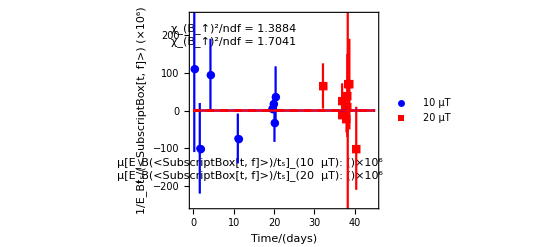

```mathematica
Show[{
EDAListPlot[pttstfet10b,pttstfet20b,PlotRange->{{-.05,45},{-250,250}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","1/E_Bt_s/(<SubscriptBox[t, f]>) (×10^6)"},PlotStyle->{Blue,Red},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.3884\nχ_(B_↑)^2/ndf = 1.7041",FontSize->Large],{10,200}],
Text[Style["μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): ()×10^6\nμ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): ()×10^6",FontSize->Large],{14,-155}]
},PlotMarkers->{Automatic,Medium}
],
EDAListPlot[pttstfet10b,pttstfet20b,PlotRange->{{-.05,45},{-200,200}},Frame->True,FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{0.018,0.018+0.105,0.018-0.105,0.010,0.010+0.095,0.010-0.095},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```

```mathematica
(*Histograms-E*)
```

{13}

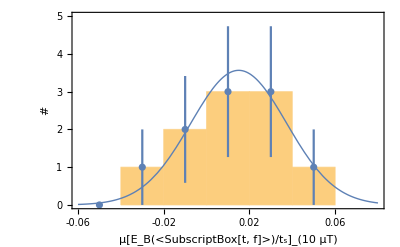

{18}

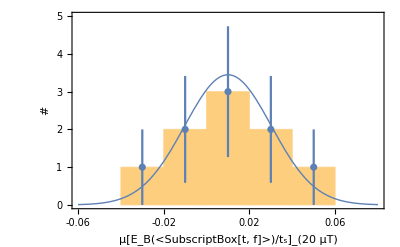

```mathematica
histe=Join[pttstfet10[[;;,2]][[;;,1]],Table[.03,{k,1,2}]];
Dimensions[histe]
inset=Show[{
Histogram[histe,{-0.06,0.06,.02}, Frame->True,FrameLabel->{"μ[E_B(<SubscriptBox[t, f]>)/t_s]_(10  μT)","#"},Axes->False,PlotRange->{{-.06,.08},{0,5}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300}],
EDAListPlot[Table[{HistogramList[histe,{-0.06,0.06,.02}][[1]][[k]]+.01,{HistogramList[histe,{-0.06,0.06,.02}][[2]][[k]],Sqrt[HistogramList[histe,{-0.06,0.06,.02}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{-0.06,0.06,.02}][[2]]][[1]]}]],
Plot[.2PDF[NormalDistribution[0.015,0.105/Sqrt[2*11]],x],{x,-0.06,0.08},PlotStyle->Thick]
},ImageSize->{800}]
histe=Join[pttstfet20[[;;,2]][[;;,1]],Table[-.03,{k,1,1}],Table[.05,{k,1,1}],Table[-.01,{k,1,1}]];
Dimensions[histe]
inset2=Show[{
Histogram[histe,{-0.04,0.06,.02}, Frame->True,FrameLabel->{"μ[E_B(<SubscriptBox[t, f]>)/t_s]_(20  μT)","#"},Axes->False,PlotRange->{{-.06,.08},{0,5}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300}],
EDAListPlot[Table[{HistogramList[histe,{-0.04,0.06,.02}][[1]][[k]]+.01,{HistogramList[histe,{-0.04,0.06,.02}][[2]][[k]],Sqrt[HistogramList[histe,{-0.04,0.06,.02}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{-0.04,0.06,.02}][[2]]][[1]]}]],
Plot[.175PDF[NormalDistribution[0.01,0.095/Sqrt[2*11]],x],{x,-0.06,0.08},PlotStyle->Thick]
},ImageSize->{800}]
```

## Histogram of Tau

InterpolatingFunction::dmval: Input value {0.204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

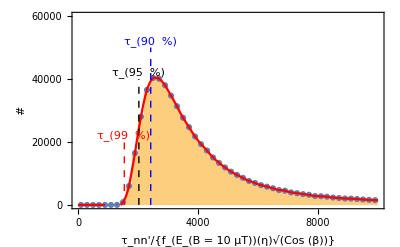

```mathematica
st=0;end=10000;int=200;multi=1000;endy=60*multi;minus=20;
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{2424,0},{2424,50*multi}}];
line2=Line[{{2029,0},{2029,40*multi}}];
line3=Line[{{1544,0},{1544,20*multi}}];
maxsz3=1000*multi;
eb10=RandomVariate[NormalDistribution[0.018*10^(-6),.105*10^(-6)],maxsz3];
eb20=RandomVariate[NormalDistribution[0.010*10^(-6),.095*10^(-6)],maxsz3];
histe=Sqrt[Select[1/eb10,#>0&]]-5minus;
datpt=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,{HistogramList[histe,{st,end,int}][[2]][[k]],Sqrt[HistogramList[histe,{st,end,int}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
datft=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,HistogramList[histe,{st,end,int}][[2]][[k]]},{k,1,end/int}];
(*
inte=BezierFunction[datft];
fit=NonlinearModelFit[datft,nn*PDF[SkewNormalDistribution[mm,ss,aa],x]+bb Exp[-tau (x-dd)],{{nn,maxsz3*10},{mm,2000},{ss,1000},{aa,3},{bb,1000},{tau,1000},{dd,1000}},x];
fit2[x_]:=int[N[(x-st)/(end-st)]][[2]];
*)
Show[{
Histogram[histe,{st,end,int}, Frame->True,FrameLabel->{"τ_nn'/{f_(E_(B = 10  μT))(η)√(Cos (β))}","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2424-minus,52*multi}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2029-minus,42*multi}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1544-minus,22*multi}],Large]}}],
EDAListPlot[datpt],
Plot[{Interpolation[datft,InterpolationOrder->2][x]},{x,st,end},PlotRange->{{st,end},{0,endy}},PlotStyle->Red]
},ImageSize->{800}]
```

FittedModel[17592.5 ⅇ^(-1.1067×10^-7 (-1976.43+x)^2) Erfc[-0.00273362 (-1976.43+x)]]

InterpolatingFunction::dmval: Input value {0.204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

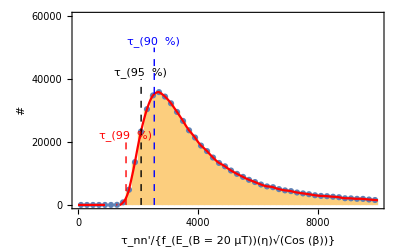

```mathematica
st=0;end=10000;int=200;multi=1000;endy=60*multi;minus=20;
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{2542,0},{2542,50*multi}}];
line2=Line[{{2104,0},{2104,40*multi}}];
line3=Line[{{1601,0},{1601,20*multi}}];
maxsz3=1000*multi;
eb10=RandomVariate[NormalDistribution[0.018*10^(-6),.105*10^(-6)],maxsz3];
eb20=RandomVariate[NormalDistribution[0.010*10^(-6),.095*10^(-6)],maxsz3];
histe=Sqrt[Select[1/eb20,#>0&]]-10minus;
datpt=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,{HistogramList[histe,{st,end,int}][[2]][[k]],Sqrt[HistogramList[histe,{st,end,int}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
datft=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,HistogramList[histe,{st,end,int}][[2]][[k]]},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
fit=NonlinearModelFit[datft,nn*PDF[SkewNormalDistribution[mm,ss,aa],x],{{nn,maxsz3*10},{mm,2000},{ss,1000},{aa,3}},x]
fit2=Fit[datft,Table[x^k,{k,-3,3,1}],x];
Show[{
Histogram[histe,{st,end,int}, Frame->True,FrameLabel->{"τ_nn'/{f_(E_(B = 20  μT))(η)√(Cos (β))}","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2542-minus,52*multi}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2104-minus,42*multi}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1601-minus,22*multi}],Large]}}],
EDAListPlot[datpt],
Plot[{Interpolation[datft,InterpolationOrder->2][x]},{x,st,end},PlotRange->{{st,end},{0,endy}},PlotStyle->Red]
},ImageSize->{800}]
```

## A

1 , Run 10 #: 12693

2 , Run 10 #: 12695

3 , Run 10 #: 12697

4 , Run 10 #: 12704

5 , Run 10 #: 12707

8 , Run 10 #: 12772

9 , Run 10 #: 12773

11 , Run 10 #: 12775

12 , Run 10 #: 12778

13 , Run 10 #: 12779

14 , Run 10 #: 12780

15 , Run 20 #: 13099

17 , Run 20 #: 13103

18 , Run 20 #: 13104

20 , Run 20 #: 13107

22 , Run 20 #: 13109

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

25 , Run 20 #: 13132

26 , Run 20 #: 13133

27 , Run 20 #: 13134

29 , Run 20 #: 13136

30 , Run 20 #: 13137

31 , Run 20 #: 13138

32 , Run 20 #: 13139

33 , Run 20 #: 13140

35 , Run 20 #: 13142

36 , Run 20 #: 13146

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.000141904 | 0.000210155 | -0.675236 | 0.516496
c | 0.00821916 | 0.0550073 | 0.149419 | 0.884517

| DF | SS | MS
Model | 2 | 0.000270103 | 0.000135052
Error | 9 | 0.000862309 | 0.0000958121
Uncorrected Total | 11 | 0.00113241 | 
Corrected Total | 10 | 0.000905994 |

1.0001

χ2_10: 1.36247

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.0000334701 | 0.000132217 | -0.253145 | 0.804115
c | -0.041077 | 0.129337 | -0.317597 | 0.755834

| DF | SS | MS
Model | 2 | 0.00360884 | 0.00180442
Error | 13 | 0.0186886 | 0.00143758
Uncorrected Total | 15 | 0.0222974 | 
Corrected Total | 14 | 0.0187807 |

1.00144

χ2_20: 0.704134

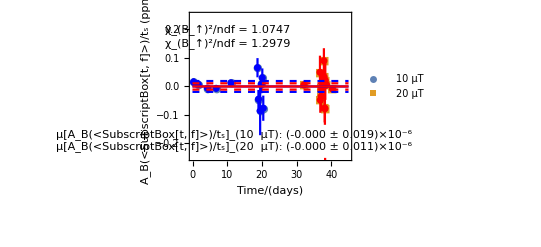

```mathematica
lvl3={};
lvl2={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl2=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],metalvl2];
If[i==1,sttime=lvl2[[1]][[1]]];
xx=((Abs[-lvl2[[1]][[1]]+lvl2[[-1]][[1]]]/2)+Abs[lvl2[[1]][[1]]-sttime])/(24*3600);
If[(!MemberQ[{6,7,10},i]&&descdat[[i]][[6]]==10)
,
Print[i," , Run 10 #: ",descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
If[((MemberQ[{15,17,18,20,22,25,26,27,29,30,31,32,33,35,36},i])&&descdat[[i]][[6]]==20)
,
Print[i," , Run 20 #: ",descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
]
nlm10=NonlinearModelFit[fttstfet10,m x + c,{m,c},x,Weights->errtstfet10];
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(√(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2))/ndim10+1]
(*20*)
nlm20=NonlinearModelFit[fttstfet20,m x + c,{m,c},x,Weights->errtstfet20];
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(√(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2))/ndim20]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.2979",FontSize->Large],{10,.15}],
Text[Style["χ_(B_↑)^2/ndf = 1.0747",FontSize->Large],{10,.2}],
Text[Style["μ[A_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): (-0.000 ± 0.019)×10^-6\nμ[A_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): (-0.000 ± 0.011)×10^-6",FontSize->Large],{12,-.19}]
},PlotMarkers->{Automatic,Medium}],
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.0245,.0245}},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{0,0.019,-0.019,0,0.011,-0.011},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```

## Histograms

FittedModel[13893.2 ⅇ^(-2.03741×10^-8 (-4550.4+x)^2) Erfc[-0.00119038 (-4550.4+x)]]

InterpolatingFunction::dmval: Input value {0.408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

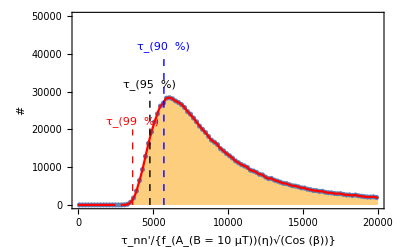

```mathematica
st=0;end=20000;multi=1000;int=200;endy=50*multi;minus=20;
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{5727,0},{5727,40*multi}}];
line2=Line[{{4793,0},{4793,30*multi}}];
line3=Line[{{3644,0},{3644,20*multi}}];
maxsz3=2000*multi;
ab10=RandomVariate[NormalDistribution[0.0*10^(-6),.019*10^(-6)],maxsz3];
ab20=RandomVariate[NormalDistribution[0.0*10^(-6),.011*10^(-6)],maxsz3];
histe=Sqrt[Select[1/ab10,#>0&]]-20minus;
datpt=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,{HistogramList[histe,{st,end,int}][[2]][[k]],Sqrt[HistogramList[histe,{st,end,int}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
datft=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,HistogramList[histe,{st,end,int}][[2]][[k]]},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
fit=NonlinearModelFit[datft,nn*PDF[SkewNormalDistribution[mm,ss,aa],x],{{nn,maxsz3*10},{mm,2000},{ss,1000},{aa,3}},x]
fit2=Fit[datft,Table[x^k,{k,-3,3,1}],x];
Show[{
Histogram[histe,{st,end,int}, Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 10  μT))(η)√(Cos (β))}","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{5727-minus,42*multi}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{4793-minus,32*multi}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{3644-minus,22*multi}],Large]}}],
EDAListPlot[datpt],
Plot[{Interpolation[datft,InterpolationOrder->2][x]},{x,st,end},PlotRange->{{st,end},{0,endy}},PlotStyle->Red]
},ImageSize->{800}]
```

FittedModel[10825.1 ⅇ^(-1.30579×10^-8 (-6134.99+x)^2) Erfc[-0.000890849 (-6134.99+x)]]

InterpolatingFunction::dmval: Input value {0.408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

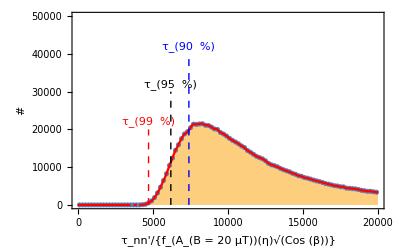

```mathematica
st=0;end=20000;int=200;multi=1000;endy=50*multi;minus=20;
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{7393,0},{7393,40*multi}}];
line2=Line[{{6188,0},{6188,30*multi}}];
line3=Line[{{4703,0},{4703,20*multi}}];
maxsz3=2000*multi;
ab10=RandomVariate[NormalDistribution[0.0*10^(-6),.019*10^(-6)],maxsz3];
ab20=RandomVariate[NormalDistribution[0.0*10^(-6),.011*10^(-6)],maxsz3];
histe=Sqrt[Select[1/ab20,#>0&]]-20minus;
datpt=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,{HistogramList[histe,{st,end,int}][[2]][[k]],Sqrt[HistogramList[histe,{st,end,int}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
datft=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,HistogramList[histe,{st,end,int}][[2]][[k]]},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
fit=NonlinearModelFit[datft,nn*PDF[SkewNormalDistribution[mm,ss,aa],x],{{nn,maxsz3*10},{mm,2000},{ss,1000},{aa,3}},x]
fit2=Fit[datft,Table[x^k,{k,-3,3,1}],x];
Show[{
Histogram[histe,{st,end,int}, Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 20  μT))(η)√(Cos (β))}","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{7393-minus,42*multi}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{6188-minus,32*multi}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{4703-minus,22*multi}],Large]}}],
EDAListPlot[datpt],
Plot[{Interpolation[datft,InterpolationOrder->2][x]},{x,st,end},PlotRange->{{st,end},{0,endy}},PlotStyle->Red]
},ImageSize->{800}]
```

{12}

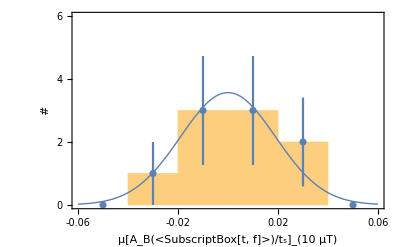

{19}

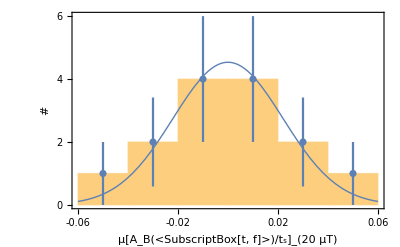

```mathematica
histe=Join[pttstfet10[[;;,2]][[;;,1]]+.005,Table[-.005,{k,1,1}]];
Dimensions[histe]
inset=Show[{
Histogram[histe,{-0.06,0.06,.02}, Frame->True,FrameLabel->{"μ[A_B(<SubscriptBox[t, f]>)/t_s]_(10  μT)","#"},Axes->False,PlotRange->{{-.06,.06},{0,6}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300}],
EDAListPlot[Table[{HistogramList[histe,{-0.06,0.06,.02}][[1]][[k]]+.01,{HistogramList[histe,{-0.06,0.06,.02}][[2]][[k]],Sqrt[HistogramList[histe,{-0.06,0.06,.02}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{-0.06,0.06,.02}][[2]]][[1]]}]],
Plot[.17PDF[NormalDistribution[0.0,0.019],x],{x,-0.06,0.06},PlotStyle->Thick]
},ImageSize->{800}]
histe=Join[pttstfet20[[;;,2]][[;;,1]]-.005,Table[-.005,{k,1,2}],Table[-.025,{k,1,1}],Table[.025,{k,1,1}]];
Dimensions[histe]
inset2=Show[{
Histogram[histe,{-0.06,0.06,.02}, Frame->True,FrameLabel->{"μ[A_B(<SubscriptBox[t, f]>)/t_s]_(20  μT)","#"},Axes->False,PlotRange->{{-.06,.06},{0,6}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300}],
EDAListPlot[Table[{HistogramList[histe,{-0.06,0.06,.02}][[1]][[k]]+.01,{HistogramList[histe,{-0.06,0.06,.02}][[2]][[k]],Sqrt[HistogramList[histe,{-0.06,0.06,.02}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{-0.06,0.06,.02}][[2]]][[1]]}]],
Plot[.25PDF[NormalDistribution[0.0,0.011*Sqrt[2*2]],x],{x,-0.06,0.06},PlotStyle->Thick]
},ImageSize->{800}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
m | 0.00127506 | 0.00433124 | 0.294386 | 0.77514
c | -0.0371809 | 0.0389978 | -0.953411 | 0.365285

| DF | SS | MS
Model | 2 | 0.000235059 | 0.00011753
Error | 9 | 0.000897353 | 0.0000997059
Uncorrected Total | 11 | 0.00113241 | 
Corrected Total | 10 | 0.000905994 |

1.0001

χ2_10: 1.36247

| Estimate | Standard Error | t-Statistic | P-Value
m | -0.00333805 | 0.00729311 | -0.457699 | 0.654724
c | -0.0393991 | 0.0840015 | -0.469029 | 0.646818

| DF | SS | MS
Model | 2 | 0.00381456 | 0.00190728
Error | 13 | 0.0184828 | 0.00142176
Uncorrected Total | 15 | 0.0222974 | 
Corrected Total | 14 | 0.0187807 |

1.00142

χ2_20: 0.704134

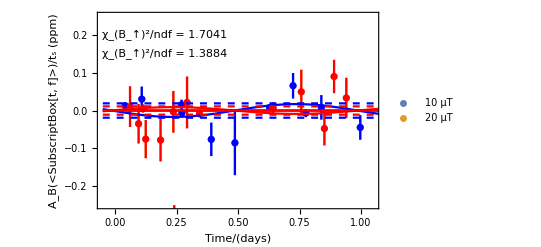

```mathematica
lvl3={};
lvl2={};
tsadd=PlusMinus[11.306,0.397];
sttime=0;
pttstfe10={};fttstfe10={};errtstfe10={};
pttstfet10={};fttstfet10={};errtstfet10={};
pttstfe20={};fttstfe20={};errtstfe20={};
pttstfet20={};fttstfet20={};errtstfet20={};
For[i=1,i≤dimdesc,i++,
lvl2=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],metalvl2];
If[i==1,sttime=lvl2[[1]][[1]]];
xx=Mod[((Abs[-lvl2[[1]][[1]]+lvl2[[-1]][[1]]]/2)+Abs[lvl2[[1]][[1]]-sttime])/(24*3600),1];
If[(!MemberQ[{6,7,10},i]&&descdat[[i]][[6]]==10)
,
(*Print["Run 10 #: ",descdat[[i]][[4]]];*)
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe10=AppendTo[pttstfe10,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe10=AppendTo[fttstfe10,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe10=AppendTo[errtstfe10,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet10=AppendTo[pttstfet10,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet10=AppendTo[fttstfet10,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet10=AppendTo[errtstfet10,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
If[((MemberQ[{15,17,18,20,22,25,26,27,29,30,31,32,33,35,36},i])&&descdat[[i]][[6]]==20)
,
(*Print["Run 20 #: ",descdat[[i]][[4]]];*)
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
ts=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
(***)
pttstfe20=AppendTo[pttstfe20,{{ts[[1]],ts[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfe20=AppendTo[fttstfe20,{ts[[1]],lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfe20=AppendTo[errtstfe20,Sqrt[ts[[2]]^2+lvl3[[1]][[2]]^2]*(descdat[[i]][[9]]*10^6/ts[[1]])];
(***)
pttstfet20=AppendTo[pttstfet20,{xx,{lvl3[[1]][[1]],lvl3[[1]][[2]]}*(descdat[[i]][[9]]*10^6/ts[[1]])}];
fttstfet20=AppendTo[fttstfet20,{xx,lvl3[[1]][[1]]}*(descdat[[i]][[9]]*10^6/ts[[1]])];
errtstfet20=AppendTo[errtstfet20,lvl3[[1]][[2]]*(descdat[[i]][[9]]*10^6/ts[[1]])];
];
]
nlm10=NonlinearModelFit[fttstfet10,m x + c,{m,c},x,Weights->errtstfet10];
ftval10={m/.nlm10["BestFitParameters"],c/.nlm10["BestFitParameters"]};
fterr10=nlm10["ParameterErrors"];
ftresidue10=nlm10["FitResiduals"];
nlm10["ParameterTable"]
nlm10["ANOVATable"]
1+nlm10["EstimatedVariance"]
ndim10=Dimensions[fttstfet10][[1]];
Print["χ2_10: ",(√(∑_(i=1)^ndim10 (pttstfet10[[i]][[2]][[1]]/pttstfet10[[i]][[2]][[2]])^2))/ndim10+1]
(*20*)
nlm20=NonlinearModelFit[fttstfet20,m x + c,{m,c},x,Weights->errtstfet20];
ftval20={m/.nlm20["BestFitParameters"],c/.nlm20["BestFitParameters"]};
fterr20=nlm20["ParameterErrors"];
ftresidue20=nlm20["FitResiduals"];
nlm20["ParameterTable"]
nlm20["ANOVATable"]
1+nlm20["EstimatedVariance"]
ndim20=Dimensions[fttstfet20][[1]];
Print["χ2_20: ",(√(∑_(i=1)^ndim20 (pttstfet20[[i]][[2]][[1]]/pttstfet20[[i]][[2]][[2]])^2))/ndim20]
Show[{
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,1.05},{-.25,.25}},PlotLegends->{"10 μT","20 μT"},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
Text[Style["χ_(B_↑)^2/ndf = 1.3884",FontSize->Large],{.2,.15}],
Text[Style["χ_(B_↑)^2/ndf = 1.7041",FontSize->Large],{.2,.2}],
Text[Style[
"[A_B(<SubscriptBox[t, f]>)/t_s]_(10  μT): {(-0.017 ± 0.238)Cos[Ωt-π/2+(0.085±0.324)] + (-0.000 ± 0.019)}×10^-6\n
[A_B(<SubscriptBox[t, f]>)/t_s]_(20  μT): {(0.009 ± 0.095)Cos[Ωt-π/2+(0.085±0.324)] + (-0.000 ± 0.011)}×10^-6
",FontSize->Medium],{.3,-.2}]
}
],
EDAListPlot[pttstfet10,pttstfet20,PlotRange->{{-.05,45},{-.0245,.0245}},Frame->True,FrameLabel->{"Time/(days)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},FrameTicks->LinTicks,PlotStyle->{Blue,Red},TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000}
],
Plot[{-.017 Sin[2Pi x+.085],.009Sin[2Pi x+.085]},{x,-.05,45},PlotStyle->{{Thick,Blue},{Thick,Red}}],
Plot[{0,0.019,-0.019,0,0.011,-0.011},{x,-.05,45},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Blue},Red,{Dashed,Red},{Dashed,Red}}]
}]
```

## Histograms

FittedModel[26577.8 ⅇ^(-2.66074×10^-7 (-1181.23+x)^2) Erfc[-0.00421771 (-1181.23+x)]]

InterpolatingFunction::dmval: Input value {0.204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

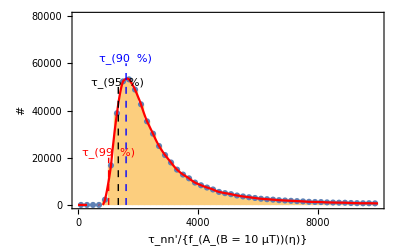

```mathematica
st=0;end=10000;int=200;multi=1000;endy=80*multi;minus=20;
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{1603,0},{1603,60*multi}}];
line2=Line[{{1343,0},{1343,50*multi}}];
line3=Line[{{1022,0},{1022,20*multi}}];
maxsz3=1000*multi;
abcos10=RandomVariate[NormalDistribution[0.017*10^(-6),.238*10^(-6)],maxsz3];
abcos20=RandomVariate[NormalDistribution[0.009*10^(-6),.095*10^(-6)],maxsz3];
histe=Sqrt[Select[1/abcos10,#>0&]]-10minus;
datpt=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,{HistogramList[histe,{st,end,int}][[2]][[k]],Sqrt[HistogramList[histe,{st,end,int}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
datft=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,HistogramList[histe,{st,end,int}][[2]][[k]]},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
fit=NonlinearModelFit[datft,nn*PDF[SkewNormalDistribution[mm,ss,aa],x],{{nn,maxsz3*10},{mm,2000},{ss,1000},{aa,3}},x]
fit2=Fit[datft,Table[x^k,{k,-3,3,1}],x];
Show[{
Histogram[histe,{st,end,int}, Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 10  μT))(η)}","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{1603-minus,62*multi}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{1343-minus,52*multi}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1022-minus,22*multi}],Large]}}],
EDAListPlot[datpt],
Plot[{Interpolation[datft,InterpolationOrder->2][x]},{x,st,end},PlotRange->{{st,end},{0,endy}},PlotStyle->Red]
},ImageSize->{800}]
```

FittedModel[17321.2 ⅇ^(-1.08724×10^-7 (-1997.81+x)^2) Erfc[-0.0027501 (-1997.81+x)]]

InterpolatingFunction::dmval: Input value {0.204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

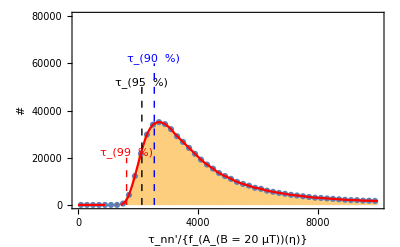

```mathematica
st=0;end=10000;int=200;multi=1000;endy=80*multi;minus=20;
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{2543,0},{2543,60*multi}}];
line2=Line[{{2129,0},{2129,50*multi}}];
line3=Line[{{1620,0},{1620,20*multi}}];
maxsz3=1000*multi;
abcos10=RandomVariate[NormalDistribution[0.017*10^(-6),.238*10^(-6)],maxsz3];
abcos20=RandomVariate[NormalDistribution[0.009*10^(-6),.095*10^(-6)],maxsz3];
histe=Sqrt[Select[1/abcos20,#>0&]]-9minus;
datpt=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,{HistogramList[histe,{st,end,int}][[2]][[k]],Sqrt[HistogramList[histe,{st,end,int}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
datft=Table[{HistogramList[histe,{st,end,int}][[1]][[k]]+int/2,HistogramList[histe,{st,end,int}][[2]][[k]]},{k,1,Dimensions[HistogramList[histe,{st,end,int}][[2]]][[1]]}];
fit=NonlinearModelFit[datft,nn*PDF[SkewNormalDistribution[mm,ss,aa],x],{{nn,maxsz3*10},{mm,2000},{ss,1000},{aa,3}},x]
fit2=Fit[datft,Table[x^k,{k,-3,3,1}],x];
Show[{
Histogram[histe,{st,end,int}, Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 20  μT))(η)}","#"},Axes->False,PlotRange->{{st,end},{0,endy}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->22],LabelStyle->{22,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{300},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2543-minus,62*multi}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2129-minus,52*multi}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1620-minus,22*multi}],Large]}}],
EDAListPlot[datpt],
Plot[{Interpolation[datft,InterpolationOrder->2][x]},{x,st,end},PlotRange->{{st,end},{0,endy}},PlotStyle->Red]
},ImageSize->{800}]
```

```mathematica
aaa=PlusMinus[0.001,.002]
1/aaa
aaa2=PlusMinus[0.001,.02]
1/aaa2
```

0.001±0.002

1000.±2000.

0.001±0.02

1000.±20000.

```mathematica
Pi/2-PlusMinus[0.085,0.324]
```

0.085±0.324

```mathematica
Sin[10+1]
Cos[10-Pi/2+1]
```

Sin[11]

Sin[11]